New Consolidation of results for computation of Classical Action of a System

```mathematica
V[x_]:=b*x+k*x^2+l*x^4+c;
```

Setting the Parameters:

```mathematica
k= -5; b=0.0; l=1; c=30;
```

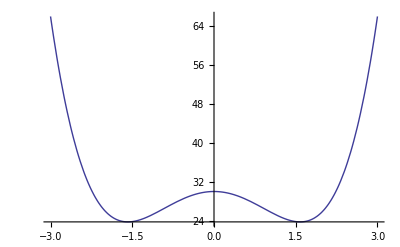

```mathematica
Plot[V[x],{x,-3,3},PlotTheme->"Classic"]
```

Extracting the large scale array for the entire spectra

```mathematica
h=0.1;
htime=0.05;

length = Floor[8/h];
time =Floor[10/htime];
xf= Array[(#-length/2 -1)*h&,{length+1}];
xi=xf
```

{-4.,-3.9,-3.8,-3.7,-3.6,-3.5,-3.4,-3.3,-3.2,-3.1,-3.,-2.9,-2.8,-2.7,-2.6,-2.5,-2.4,-2.3,-2.2,-2.1,-2.,-1.9,-1.8,-1.7,-1.6,-1.5,-1.4,-1.3,-1.2,-1.1,-1.,-0.9,-0.8,-0.7,-0.6,-0.5,-0.4,-0.3,-0.2,-0.1,0.,0.1,0.2,0.3,0.4,0.5,0.6,0.7,0.8,0.9,1.,1.1,1.2,1.3,1.4,1.5,1.6,1.7,1.8,1.9,2.,2.1,2.2,2.3,2.4,2.5,2.6,2.7,2.8,2.9,3.,3.1,3.2,3.3,3.4,3.5,3.6,3.7,3.8,3.9,4.}

```mathematica
For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,


s=NDSolve[{Xcl''[u]+V'[Xcl[u]]==0,Xcl[0]== xi[[i]] ,Xcl[time*htime]== xf[[j]]},Xcl[u],{u,0,time*htime}];

Subscript[A, i,j]=(Flatten[Table[Xcl[u]/.s,{u,0,Floor[time*htime],htime}]]);
]
]
```

NDSolve::berr: The scaled boundary value residual error of 4.39666 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 1.02888 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

NDSolve::berr: The scaled boundary value residual error of 1.69223 indicates that the boundary values are not satisfied to specified tolerances. Returning the best solution found.

General::stop: Further output of NDSolve::berr will be suppressed during this calculation.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

FindRoot::cvmit: Failed to converge to the requested accuracy or precision within 100 iterations.

General::stop: Further output of FindRoot::cvmit will be suppressed during this calculation.

FindRoot::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the function value is still greater than the tolerance prescribed by the AccuracyGoal option.

General::stop: Further output of FindRoot::sszero will be suppressed during this calculation.

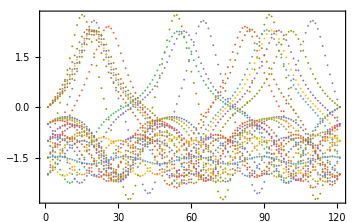

```mathematica
ListPlot[{
Subscript[A, 1,1],Subscript[A, 1,2],Subscript[A, 1,3],Subscript[A, 1,4],Subscript[A, 1,5],
Subscript[A, 2,1],Subscript[A, 2,2],Subscript[A, 2,3],Subscript[A, 2,4],Subscript[A, 2,5],
Subscript[A, 3,1],Subscript[A, 3,2],Subscript[A, 3,3],Subscript[A, 3,4],Subscript[A, 3,5],
Subscript[A, 4,1],Subscript[A, 4,2],Subscript[A, 4,3],Subscript[A, 4,4],Subscript[A, 4,5],
Subscript[A, 5,1],Subscript[A, 5,2],Subscript[A, 5,3],Subscript[A, 5,4],Subscript[A, 5,5]
},Frame->True,FrameStyle->Directive[GrayLevel[0],Thickness[Medium]],ImageSize->Medium, PlotStyle->Thick]
```

It Kind of shows the classical density (we can attempt for a better plot at some point)


Now we wish to compute the Classical Action;

```mathematica
L=ConstantArray[0,{length+1, length+1,time}];
S=ConstantArray[0,{length+1, length+1,time}];
Psi=ConstantArray[0,{length+1, time}];



For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

L[[i,j,t]]= (Subscript[A, i,j][[t]]-Subscript[A, i,j][[t-1]])^2/(2*htime*htime)-V[Subscript[A, i,j][[t]]]; 
]
]
]


For[i=1,i<length+2,i++,
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

S[[i,j,t]]= htime*Sum[L[[i,j,u]],{u,t}]; 
]
]
]
```

The other factors;

```mathematica
Phi=ConstantArray[0,{length-1, length-1,time}];
Phi2=ConstantArray[0,{length-1, length-1,time}];


For[i=1,i<length,i++,
For[j=1,j<length,j++,
For[t=2,t<time,t++,

Phi[[i,j,t]]= htime*Sum[Sqrt[V''[Subscript[A, i-1,j-1][[u]]]],{u,t}]; 
]
]
]

For[i=1,i<length,i++,
For[j=1,j<length,j++,
For[t=2,t<time,t++,

Phi2[[i,j,t]]= htime*Sum[1/V''[Subscript[A, i+1,j+1][[u]]],{u,t}]; 
]
]
]
```

Part::partw: Part 4 of A_(0,0) does not exist.

Part::partw: Part 5 of A_(0,0) does not exist.

General::stop: Further output of Part::partw will be suppressed during this calculation.

Import Export Business:

```mathematica
Export["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Scl_4_0.5.mat",S]
```

C:\Users\Ritam\Documents\Wolfram Mathematica\Scl_4_0.5.mat

```mathematica
S=Import["C:\\Users\\Ritam\\Documents\\Wolfram Mathematica\\Scl_4_0.5.mat"];
```

Checking the Dimensions:

```mathematica
Dimensions[S]
```

{9,9,120}

```mathematica
Dimensions[SImp]
```

{1,9,9,120}

Initial Conditions:

```mathematica
sigma=1.0;
aorigin=2.1;
Gauss[x_]:= 1/(Sqrt[2*Pi]*sigma)Exp[-1/2*((x-aorigin)/sigma)^2]
```

Finding the wavefunction:

```mathematica
For[j=1,j<length+2,j++,
For[t=2,t<time,t++,

Psi[[j,t]]= h*1/Sqrt[2*Pi*I*t*htime] Sum[Exp[I*S[[1,i,j,t]]]*Gauss[xi[[i]]],{i,length+1}]; 
]
]
```

Plots:

```mathematica
MatrixPlot[Abs[Psi]^2,Mesh->All,MeshStyle->Directive[Gray,Dashed], ImageSize->Full, PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
MatrixPlot[Abs[Psi]^2,Mesh->All,MeshStyle->Directive[Gray,Dashed], ImageSize->Full, PlotTheme->"Detailed"]
```

-Graphics-

```mathematica
MatrixPlot[Abs[Psi]^2,Mesh->All,MeshStyle->Directive[Gray,Dashed], ImageSize->Full, PlotTheme->"Detailed"]
```

-Graphics-